```mathematica
(* Putting in required known constants *)
M = 1.2209*10^19 ;(* Non-reduced Planck Mass in GeV/c^2 *)
(*M = 1*)
δ = 4.5*10^-5 ;(*I think this is the current value I'm using*)
```

```mathematica
(* Potential, without normalization *)
V[θ_] = θ^4; (* θ is ϕ/M *)

(* Slow-roll parameters *)
(*H[θ_]=√((8 π)/(3 M^2)V[θ]);*)
ϵ[ϕ_] = 1/(16 π)(V'[ϕ]/V[ϕ])^2;
(* Field Value at the end of inflation *)
θe = Re[x/. FindRoot[ϵ[x]==1,{x,1}]]
Nume[θ_?NumberQ]:=Re[(8 π) NIntegrate[V[x]/V'[x],{x, θe,θ}]]

(* Field value NN e-folds before the end of inflation. Exact answer: *)
θN[NN_] := Re[x/. FindRoot[Nume[x] == NN, {x,θe}]]

(* Normalization *)
Vend[NN_]:= (3 δ^2)/(128π)(V'[θN[NN]]/V[θN[NN]])^2(V[θe]/V[θN[NN]])

(* Reheat Temperature *)
Trh[NN_]:=Vend[NN]^(1/4)

(* Max N *)
NM = Re[x/. FindRoot[x-Log[Trh[x]]==68,{x,60}]]
```

0.56419

62.3326

```mathematica
ϕN[60]
```

5.37985×10^19

```mathematica
Vend[60]
```

7.43339×10^61

```mathematica
(Vend[60])^(1/4)
```

2.93628×10^15

```mathematica
Trh[60]
```

2.93628×10^15

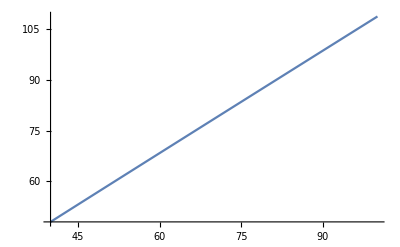

Syntax::bktmop: Expression "x-Log[Trh[x]/M],{x,40,100}]" has no opening "[".

```mathematica
Plot[x-Log[Trh[x]],{x,40,100}]
```

```mathematica
NSolve[x-Log[Trh[x]/M]==68, x]
```

{{x→127.815}}

```mathematica
x/.{x->{127.81487882613234,127.81487882613234}}
```

{127.815,127.815}

```mathematica
fff[x_] := x-Log[Trh[x]] 
fff[59.67]
fff[62.3326]
```

67.9987

70.6935

```mathematica
NSolve[fff[x]  == 68, x]
```

{{x→127.815}}

```mathematica
59.67 * 2.1415926
```

127.789

```mathematica
62.3326-59.67
```

2.6626